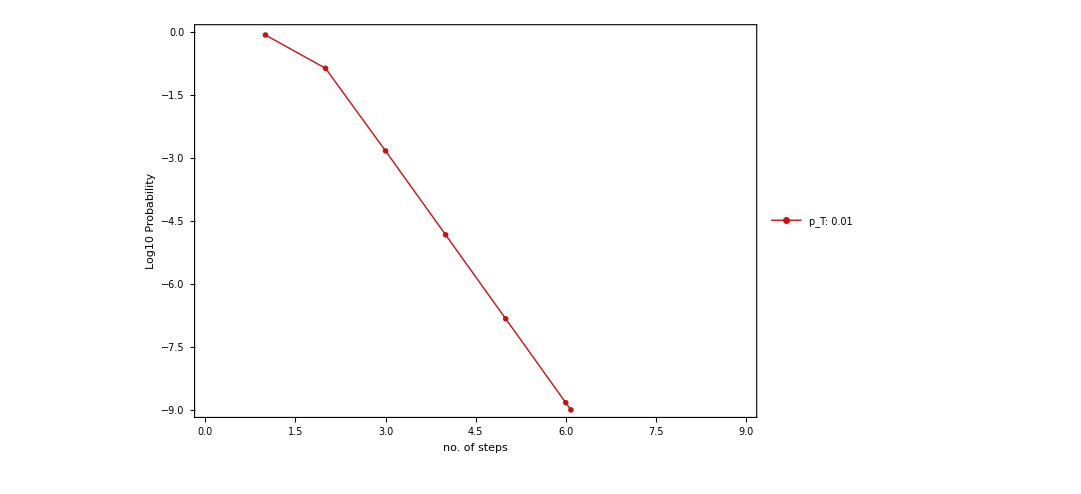

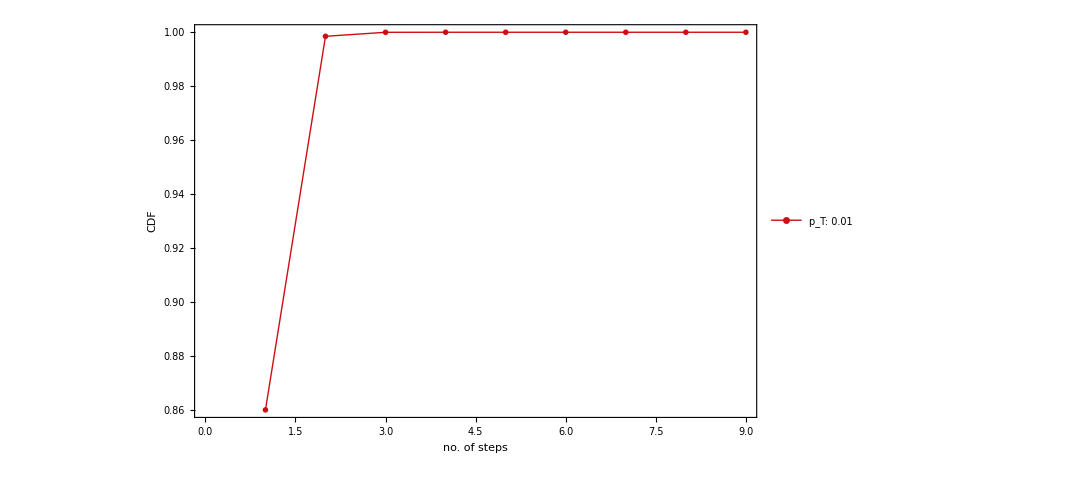

ColorData::notent: 115 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: Directive[AbsoluteThickness[1], 115] is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: {AbsoluteThickness[1], 115} is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData :: notent will be suppressed during this calculation.

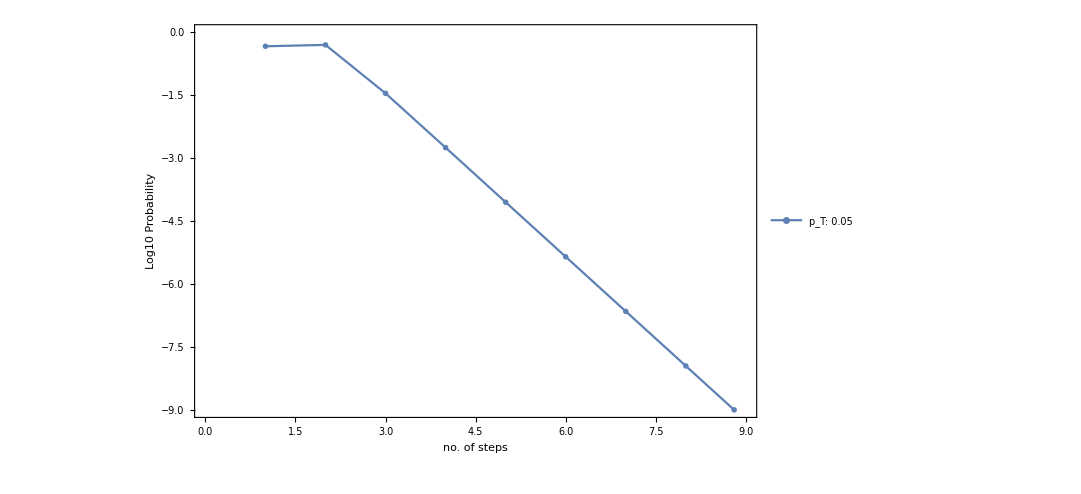

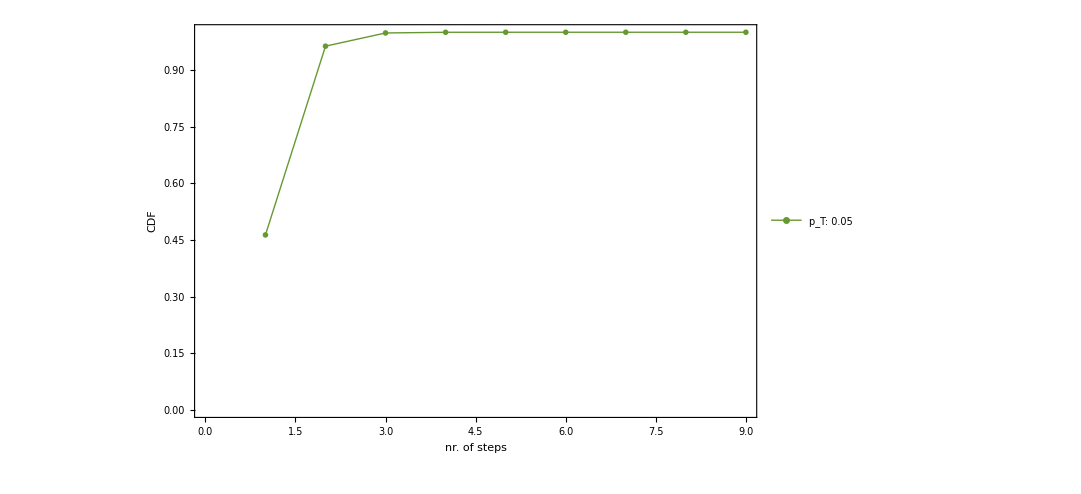

ColorData::notent: RGBColor[0, 0, 1] is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: AbsoluteThickness[1], InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[0, 0, 1], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.`, 0.`, 0.6666666666666666`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[ is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: AbsoluteThickness[1]RGBColor[0, 0, 1] is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData :: notent will be suppressed during this calculation.

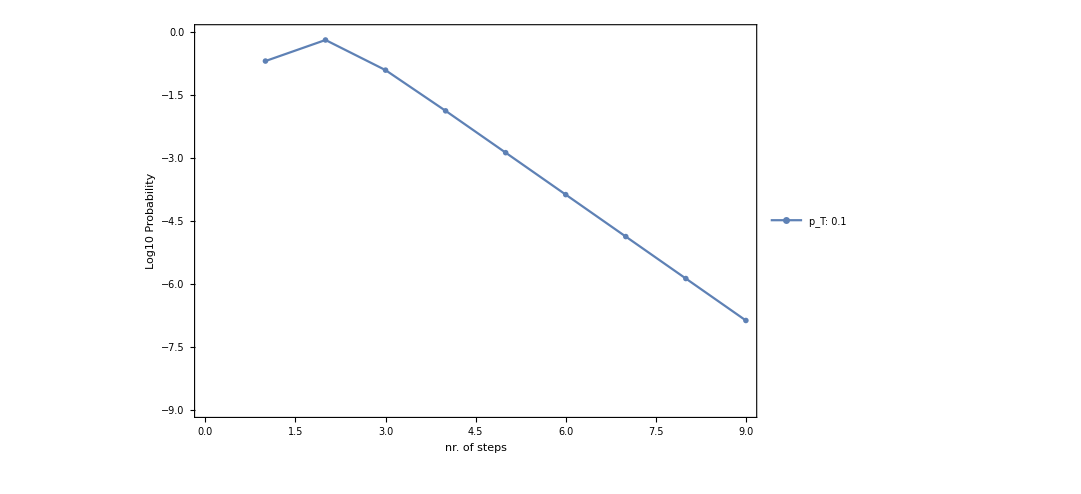

ColorData::notent: 115 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: Directive[AbsoluteThickness[1], 115] is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: {AbsoluteThickness[1], 115} is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData :: notent will be suppressed during this calculation.

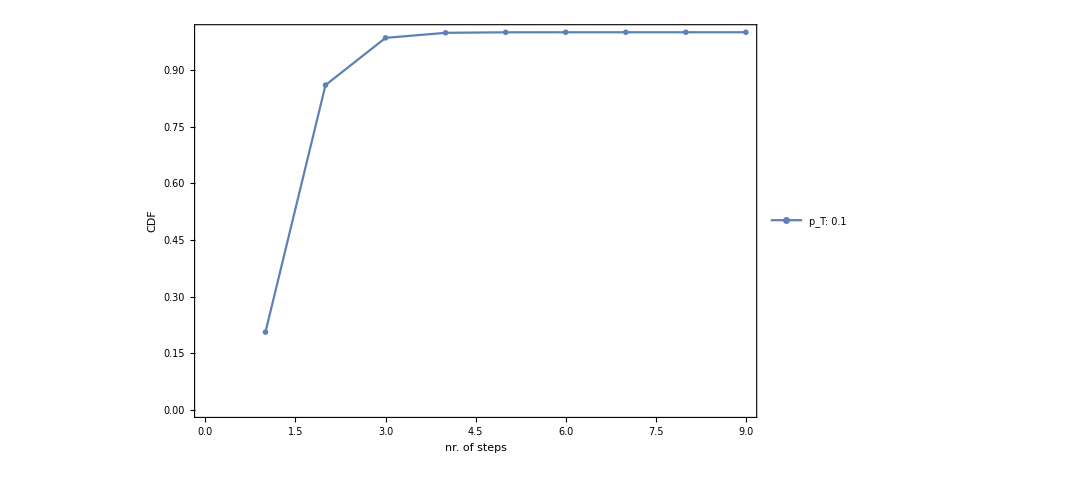

28.3465

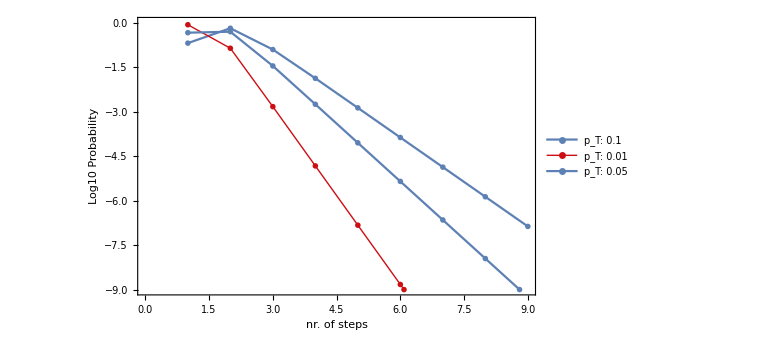

PMF.eps

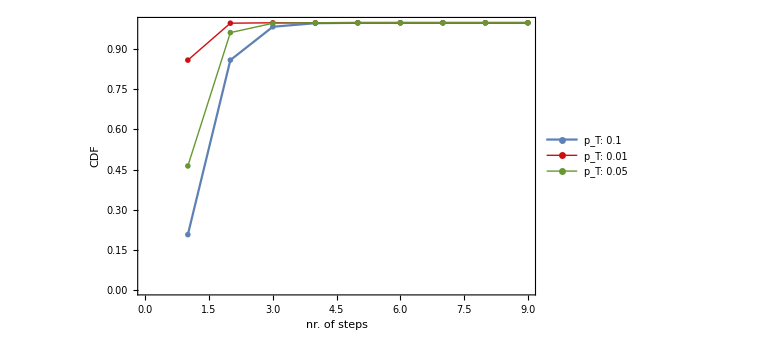

CDF.eps

```mathematica
(*
 DO:
 - no collision-related losses;
  - losses of retransmission requests due to wireless medium;
  - losses of informational packets due to wireless medium
GET:
- PMF on the number of retr. attempts to deliver a packet and message to all the stations;
  - PMF and CDF of the delay;
  - mean delay till all get the packet;
*)

(* Maxumun number of retransmissions, assumed to be infinity but this is enough *)
stepsMax=10;

(* Range of packet loss values *)
Pinit=0.01;
Pend  =0.1;
Pstep=0.01;

(* Number of stations *)
Ninit=15;
Nend=15;
Nstep=15;

(* Loss probability of retransmission packet *)

Unprotect[Power];
Power[0,0]=1;
Protect[Power];

pR=0;

(*Time to transmit the data packet (Tt) and retrnamission request (Tq), respectively, Tq<<Tt as data packets is usually longer *)
Tt= 0.01;
Tq= 0.001;

(* Time to wait to get the packet of interest as a result of the sent request *)

Tconst = 0.01;

(* Arrays to store PDF, CDF, Variance, Mean and quantile of the number of steps till absorbtion *)
singlePMFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleCDFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];

singleVarArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];
singleMeanArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Arrays to store PDF, Mean and quantile of delay till absorbtion *)
singlePMFDelay=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleMeanDelay=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Definiting Binomial distribution *)
BD[n_,p_,i_]:=Binomial[n,i]*(p^i)*(1-p)^n/(1-p)^i;

i=1;
j=1;

Do[
Do[

(* PARAMETERIZATION *)

(* Matrix Q of the absorbing Markov chain chain: jumping between transient states *)
Q=Table[0*k*n,{n,1,currN},{k,1,currN}];


For[n=1,n<currN+1,n++,
For[k=1,k<currN+1,k++,
If[k==n,If[n==currN,Part[Q,n,k]=Power[currP,n],Part[Q,n,k]=Power[pR,currN-n]+(1-Power[pR,currN-n])*Power[currP,n]]];
If[k<n,If[n==currN,Part[Q,n,k]=BD[n,currP,k],Part[Q,n,k]=(1-Power[pR,currN-n])*BD[n,currP,k]]];
];
];

(* Print["Matrix Q: ",TableForm[Q]]; *)

(* Defining vector t of the chain: absorbtion from every state *)
t=Table[0*n,{n,1,currN}];

For[n=1,n<currN+1,n++,
If[n≠currN,Part[t,n]=(1-Power[pR,currN-n])*(Power[1-currP,n]),Part[t,n]=Power[1-currP,currN]];
];

(* Print["vector t: ",TableForm[t]]; *)

(* Defining initial state probability vector: we always start with N stations not having a packet *)
v=Table[0*n,{n,1,currN}];
Part[v,currN]=1;

(* Print["vector v: ",TableForm[v]]; *)

(* COMPUTING METRICS FOR A SINGLE PACKET *)

(* Supplementary entities *)
e=Table[0*n+1,{n,1,currN}];

(* Print["vector e: ",TableForm[e]]; *)

(* PMF of the number of steps till absrobtion: gives PMF of the delay *)
stepsPMF=Table[v.If[n≠0,MatrixPower[Q,n],IdentityMatrix[currN]].t,{n,0,stepsMax}];

(* Print["stepsPMF: ",TableForm[stepsPMF]]; *)

(* Testing whether PMF sums up to one, if not increase the stepsMax*)
If[Sum[Part[stepsPMF,n],{n,0,stepsMax}]<0.99||Sum[Part[stepsPMF,n],{n,0,stepsMax}]>1.01,Print["PMF does not sum up to 1!"]];

(* Print["PMF sum to 1? ",TableForm[Sum[Part[stepsPMF,n],{n,1,stepsMax}]]]; *)

(* CDF of the number of steps till absrobtion: gives CDF of the delay *)

stepsCDF=Table[Sum[Part[stepsPMF,n],{n,1,k}],{k,1,stepsMax}];
(* Mean number of steps before absorbtion: gives mean delay *)
stepsMean=Sum[Part[stepsPMF,n]*n,{n,1,stepsMax}];

(* Print["steps Mean: ",TableForm[stepsMean]]; *)

(* Variance of the number of steps *)
stepsVar=Sum[Part[stepsPMF,n]*Power[(n-stepsMean),2],{n,1,stepsMax}];

(* Print["steps Variance: ",TableForm[stepsVar]]; *)

(* We can also get probabilities that k, k=1,2,..,N stations not having a packet after k step this is a vector: v*Q^{k} *)

(* Computing the Fundamental matrix *)
Z=Inverse[IdentityMatrix[currN]-Q];

(* Computing hi as the probability of being in the arbitrary state i after original transmission of the packet *)
(*h =Table [ PDF[BinomialDistribution[currN,pR],n],{n,0,currN}];*)

(* Probability of visiting a transient state j when starting in transient state i *)
Zdq=DiagonalMatrix[Diagonal[Z]];
visitPrMatrix=(Z-IdentityMatrix[currN]).Inverse[Zdq];

 (* Print["Matrix Z: ",TableForm[Z]]; *)

(* Print["Visits V: ",TableForm[visitPrMatrix]]; *)

(* CONDITIONAL DELAY IN A CERTAIN STATE *)
(* Array for conditional delays for failure and overall *)
condDelayFail=Table[0,{k,1,currN}];
condDelayAll=Table[0,{k,1,currN}];

(* Computing conditional delays for states starting from 1 to N-1: in case of failure *)
For [n=1,n<currN+1,n++,
  Part[condDelayFail,n] = Tconst;
];


(*
For [i=1,i<currN+1,i++,
 Print["Conditional delay fail ",i,":",TableForm[Part[condDelayFail,i]]];
];
*)


(* Computing the mean delay in the arbitrary state i *)
For [n=1,n<currN+1,n++,
Part[condDelayAll,n]= 1/Part[Q,n,n]*Part[condDelayFail,n]+ (Tq * (1-Power[pR,currN-n]) )+( Tt * (1-Power[currP,n]));
];

(*
For [i=1,i<currN+1,i++,
 Print["Conditional delay all ",i,": ",TableForm[Part[condDelayAll,i]]];
];
*)

(* Computing the mean delay till absorption *)

overallDelay =Tt + Sum[Part[condDelayAll,k]*Part[visitPrMatrix,n,k],{n,1,currN},{k,1,n}];

(* Print["Overall Delay: ",TableForm[overallDelay]]; *)

(* Storing PMF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singlePMFArray,i,j,2,n]=Part[stepsPMF,n];
Part[singlePMFArray,i,j,1,n]=n;
];

(* Print["PMF of steps till absorption: ",TableForm[singlePMFArray]]; *)

(* Storing CDF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singleCDFArray,i,j,2,n]=Part[stepsCDF,n];
Part[singleCDFArray,i,j,1,n]=n;
];

(* Print["CDF of steps till absorption: ",TableForm[singleCDFArray]]; *)

(* Storing Variance of the number of steps to global matrices*)
Part[singleVarArray,i,j]=stepsVar;
(* Print["Variance of steps till absorption: ",TableForm[singleVarArray]]; *)


(* Storing Mean of the number of steps to global matrices*)
Part[singleMeanArray,i,j]=stepsMean;
(* Print["Mean of the number of steps till absorption: ",TableForm[singleMeanArray]]; *)


(* Storing Mean of the delay to global matrices*)
Part[singleMeanDelay,i,j]=overallDelay;
(* Print["Mean of the delay till absorption: ",TableForm[singleMeanDelay]]; *)

(* PMF and CDF of delay not for this version *)



(* ENDING THE CYCLES *)
i++;,
{currP,Pinit,Pend,Pstep}];

i=1;
j++;,


{currN,Ninit,Nend,Nstep}];


markers1 = {{-Graphics-, 0.04}};

kplot=ListPlot[Evaluate[Log[10,{Part[singlePMFArray,1,1,2,1],Part[singlePMFArray,1,1,2,2],Part[singlePMFArray,1,1,2,3],Part[singlePMFArray,1,1,2,4],Part[singlePMFArray,1,1,2,5],Part[singlePMFArray,1,1,2,6],Part[singlePMFArray,1,1,2,7],Part[singlePMFArray,1,1,2,8],Part[singlePMFArray,1,1,2,9]}],PlotMarkers->markers1,Frame->True ,FrameLabel->{Style["no. of steps",Black,Large],Style["Log10 Probability",Black,Large]},PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[35,"ColorList"]),ImageSize->800,AxesOrigin->{0,0},Joined->True,PlotRange->{-9,0},PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.01"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.1],20}],{0.87,0.93}]],BaseStyle->{FontSize->25}]
(*
kkplot=ListPlot[Evaluate[Log[10,{Part[singleCDFArray,1,1,2,1],Part[singleCDFArray,1,1,2,2],Part[singleCDFArray,1,1,2,3],Part[singleCDFArray,1,1,2,4],Part[singleCDFArray,1,1,2,5],Part[singleCDFArray,1,1,2,6],Part[singleCDFArray,1,1,2,7],Part[singleCDFArray,1,1,2,8],Part[singleCDFArray,1,1,2,9]}],PlotMarkers->markers1,Frame->True ,FrameLabel->{Style["no. of steps",Black,Large],Style["CDF",Black,Large]},PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[85,"ColorList"]),ImageSize->800,AxesOrigin->{0,0},Joined->True,PlotRange->{-1,0},PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.01"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.1],20}],{0.87,0.93}]],BaseStyle->{FontSize->25}]
*)

kkplot=ListPlot[Evaluate[{Part[singleCDFArray,1,1,2,1],Part[singleCDFArray,1,1,2,2],Part[singleCDFArray,1,1,2,3],Part[singleCDFArray,1,1,2,4],Part[singleCDFArray,1,1,2,5],Part[singleCDFArray,1,1,2,6],Part[singleCDFArray,1,1,2,7],Part[singleCDFArray,1,1,2,8],Part[singleCDFArray,1,1,2,9]},PlotMarkers->markers1,Frame->True ,FrameLabel->{Style["no. of steps",Black,25],Style["CDF",Black,25]},PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[35,"ColorList"]),ImageSize->800,AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.01"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->18,LabelStyle->{GrayLevel[0.1],22}],{0.87,0.85}]],BaseStyle->{FontSize->26}]


markers2 = { {-Graphics-, 0.04}};

splot=ListPlot[Evaluate[Log[10,{Part[singlePMFArray,5,1,2,1],Part[singlePMFArray,5,1,2,2],Part[singlePMFArray,5,1,2,3],Part[singlePMFArray,5,1,2,4],Part[singlePMFArray,5,1,2,5],Part[singlePMFArray,5,1,2,6],Part[singlePMFArray,5,1,2,7],Part[singlePMFArray,5,1,2,8],Part[singlePMFArray,5,1,2,9]}],PlotMarkers->markers2,Frame->True ,FrameLabel->{Style["no. of steps",Black,Large],Style["Log10 Probability",Black,Large]},PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[115,"ColorList"]),ImageSize->800,AxesOrigin->{0,0},Joined->True,PlotRange->{-9,0},PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.05"#}]&/@Range[4],LegendMarkers->markers2,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.1],20}],{0.87,0.75}]],BaseStyle->{FontSize->25}]
(*
ssplot=ListPlot[Evaluate[Log[10,{Part[singleCDFArray,5,1,2,1],Part[singleCDFArray,5,1,2,2],Part[singleCDFArray,5,1,2,3],Part[singleCDFArray,5,1,2,4],Part[singleCDFArray,5,1,2,5],Part[singleCDFArray,5,1,2,6],Part[singleCDFArray,5,1,2,7],Part[singleCDFArray,5,1,2,8],Part[singleCDFArray,5,1,2,9]}],PlotMarkers->markers2,Frame->True ,FrameLabel->{Style["no. of steps",Black,Large],Style["CDF",Black,Large]},PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[75,"ColorList"]),ImageSize->800,AxesOrigin->{0,0},Joined->True,PlotRange->{-1,0},PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.05"#}]&/@Range[4],LegendMarkers->markers2,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.1],20}],{0.87,0.83}]],BaseStyle->{FontSize->25}]
*)

ssplot=ListPlot[Evaluate[{Part[singleCDFArray,5,1,2,1],Part[singleCDFArray,5,1,2,2],Part[singleCDFArray,5,1,2,3],Part[singleCDFArray,5,1,2,4],Part[singleCDFArray,5,1,2,5],Part[singleCDFArray,5,1,2,6],Part[singleCDFArray,5,1,2,7],Part[singleCDFArray,5,1,2,8],Part[singleCDFArray,5,1,2,9]},PlotMarkers->markers2,Frame->True ,FrameLabel->{Style["nr. of steps",Black,25],Style["CDF",Black,25]},PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[65,"ColorList"]),ImageSize->800,AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.05"#}]&/@Range[4],LegendMarkers->markers2,LegendMarkerSize->18,LabelStyle->{GrayLevel[0.1],22}],{0.87,0.75}]],BaseStyle->{FontSize->26}]

markers3 = { {-Graphics-, 0.04}};

cplot=ListPlot[Evaluate[Log[10,{Part[singlePMFArray,10,1,2,1],Part[singlePMFArray,10,1,2,2],Part[singlePMFArray,10,1,2,3],Part[singlePMFArray,10,1,2,4],Part[singlePMFArray,10,1,2,5],Part[singlePMFArray,10,1,2,6],Part[singlePMFArray,10,1,2,7],Part[singlePMFArray,10,1,2,8],Part[singlePMFArray,10,1,2,9]}],PlotMarkers->markers3,Frame->True ,FrameLabel->{Style["nr. of steps",Black,Large],Style["Log10 Probability",Black,Large]},PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[Blue,"ColorList"]),ImageSize->800,AxesOrigin->{0,0},Joined->True,PlotRange->{-9,0},PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.1"#}]&/@Range[4],LegendMarkers->markers3,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.1],20}],{0.86,0.73}]],BaseStyle->{FontSize->25}]
(*
ccplot=ListPlot[Evaluate[Log[10,{Part[singleCDFArray,10,1,2,1],Part[singleCDFArray,10,1,2,2],Part[singleCDFArray,10,1,2,3],Part[singleCDFArray,10,1,2,4],Part[singleCDFArray,10,1,2,5],Part[singleCDFArray,10,1,2,6],Part[singleCDFArray,10,1,2,7],Part[singleCDFArray,10,1,2,8],Part[singleCDFArray,10,1,2,9]}],PlotMarkers->markers3,Frame->True ,FrameLabel->{Style["no. of steps",Black,Large],Style["CDF",Black,Large]},PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[Blue,"ColorList"]),ImageSize->800,AxesOrigin->{0,0},Joined->True,PlotRange->{-1,0},PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.1"#}]&/@Range[4],LegendMarkers->markers3,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.1],20}],{0.86,0.73}]],BaseStyle->{FontSize->25}]
*)

ccplot=ListPlot[Evaluate[{Part[singleCDFArray,10,1,2,1],Part[singleCDFArray,10,1,2,2],Part[singleCDFArray,10,1,2,3],Part[singleCDFArray,10,1,2,4],Part[singleCDFArray,10,1,2,5],Part[singleCDFArray,10,1,2,6],Part[singleCDFArray,10,1,2,7],Part[singleCDFArray,10,1,2,8],Part[singleCDFArray,10,1,2,9]},PlotMarkers->markers3,Frame->True ,FrameLabel->{Style["nr. of steps",Black,25],Style["CDF",Black,25]},PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[115,"ColorList"]),ImageSize->800,AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.1"#}]&/@Range[4],LegendMarkers->markers3,LegendMarkerSize->18,LabelStyle->{GrayLevel[0.1],22}],{0.86,0.65}]],BaseStyle->{FontSize->26}]



cm=72/2.54 (*centimetres*)
Show[cplot,kplot,splot,ImageSize->20 cm]
Export["PMF.eps",Show[splot,kplot,cplot,ImageSize->20 cm]]

Show[ccplot,kkplot,ssplot,ImageSize->20 cm]
Export["CDF.eps",Show[ssplot,kkplot,ccplot,ImageSize->20 cm]]
```